```mathematica
P[ n_, k_ ] := Sum[ 1/k - P[n/j, k+1], {j,2,n}]
```

```mathematica
Table[P[x,1] - Sum[ PrimePi[ x^(1/k) ]/k, {k,1, 30}], {x,1,100}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ChebPsi[ n_ ] := Sum[ Log[j] - ChebPsi[n/j], {j,2,n}]
```

```mathematica
Table[N[ChebPsi[x]-Sum[ MangoldtLambda[ j ], {j,2,x}]] , {x,2,100}]
```

{0.,0.,0.,0.,0.,0.,0.,-8.88178×10^-16,0.,0.,0.,0.,0.,-1.77636×10^-15,0.,0.,1.77636×10^-15,1.77636×10^-15,-3.55271×10^-15,3.55271×10^-15,-3.55271×10^-15,-3.55271×10^-15,-3.55271×10^-15,0.,0.,-3.55271×10^-15,0.,0.,0.,0.,0.,0.,-7.10543×10^-15,0.,0.,0.,0.,0.,0.,0.,7.10543×10^-15,7.10543×10^-15,0.,0.,0.,0.,0.,0.,0.,-1.42109×10^-14,-1.42109×10^-14,-1.42109×10^-14,0.,-1.42109×10^-14,1.42109×10^-14,0.,0.,0.,0.,0.,0.,-1.42109×10^-14,0.,1.42109×10^-14,-1.42109×10^-14,-1.42109×10^-14,-2.84217×10^-14,0.,-1.42109×10^-14,-1.42109×10^-14,0.,0.,0.,0.,0.,-1.42109×10^-14,1.42109×10^-14,1.42109×10^-14,0.,1.42109×10^-14,0.,0.,0.,0.,-2.84217×10^-14,-2.84217×10^-14,0.,0.,0.,0.,2.84217×10^-14,0.,0.,0.,0.,0.,0.,-2.84217×10^-14,-2.84217×10^-14}

```mathematica
DD[n_,1] := Floor[n]-1
DD[n_,k_] := Sum[ DD[n/j, k-1], {j,2,n}]
PP[ n_ ] := Sum[ (-1)^(k+1) / k DD[ n, k ], {k, 1, Log[2, n] }]
Table[PP[x] - Sum[ PrimePi[ x^(1/k) ]/k, {k,1, 30}], {x,2,100}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
D2[n_, a_, 0 ] := 1
D2[n_,a_, 1 ] := Floor[n] - a + 1
D2[ n_, a_, k_ ] := Sum[ Sum[  Binomial[k, j ]  D2[ n/( m^(k-j) ), m+1, j], {j,0, k-1}], {m, a, n^(1/k)}]
P2[ n_ ] := Sum[ (-1)^(k+1) / k D2[ n, 2, k ], {k, 1, Log[2, n] }]
Table[P2[x] - Sum[ PrimePi[ x^(1/k) ]/k, {k,1, 30}], {x,2,100}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
D2[100,2,2]
```

283

```mathematica
FF[n_, a_] := (Floor[ n^(1/2)]^2 + Floor[n^(1/2)] - a^2 + a)/2
```

```mathematica
N[FF[100,6]]
```

40.

```mathematica
Sum[ m, {m,6,Floor[ 100^(1/2) ]}]
```

40

```mathematica
Sum[ n/m, {m,2,Floor[n^(1/2)]}]
```

n (-1+HarmonicNumber[Floor[√n]])

```mathematica
F2[ n_, a_] := -(Floor[n^(1/2)]^2) + a^2 - 2a + 1 + 2 Sum[ Floor[ n/m], {m,a,n^(1/2)}]
```

```mathematica
F2[100,3]
```

186

```mathematica
N[1 - (Floor[ 100^(1/2)]^2) + 2Sum[ Floor[ 100/m], {m,2, 100^(1/2)}]]
```

283.

```mathematica
F3[ n_, a_] := -(Floor[n^(1/2)]^2) + a^2 - 2a +1 + 2n(HarmonicNumber[ Floor[ n^(1/2)] ] - HarmonicNumber[ a-1]) + -2Sum[FractionalPart[ n/m], {m,a, n^(1/2)}]
```

```mathematica
N[F3[100,2]]
```

283.

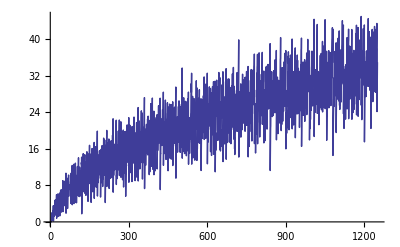

```mathematica
Plot[ 2Sum[FractionalPart[ n/m], {m,2, n^(1/2)}], {n,1,1250}]
```

```mathematica
D3[n_, a_, 0 ] := 1
D3[n_,a_, 1 ] := Floor[n] - a + 1
```

```mathematica
D3[ n_, a_, k_ ] := Sum[ Sum[  Binomial[k, j ]  (-1)^(k-j+1) D3[ n/( m^(k-j) ), m, j], {j,0, k-1}], {m, a, n^(1/k)}]
```

```mathematica
D3[ 100, 3,3]
```

71

```mathematica
D2[100,3,3]
```

71